## Instructions

Please enter your student number into the following cell:

{Put your student number here}

Save and name this Notebook as your student number using File ⊳ Save As… 

⚠ Make sure that you save your Notebook to the server in the Mathematics Computing Laboratory, or to a memory stick, in case your computer crashes.

Save your work regularly during the course of the exam.

This is an “open-book” exam. You are permitted to bring in printed or electronic copies of your lecture notes and assignment solutions, and to access electronic resources such as the Documentation Center and the internet. 

⚠ Spoken or electronic communication via email, messaging, chat, file transfer, etc. is not permitted. Such action may result in your being deprived of any credit for this examination or even, in some cases, for the whole unit. This will apply regardless of whether the material has been used at the time it is found.

Insert your solutions—both Mathematica code and text—directly into the Notebook immediately following the part of the question that you are answering.

Text should be inserted in the StudentAnswer style, which looks like this, using the Style drop-down menu.

Upload your solutions to the Exam folder on the Physics FTP server.

## Questions

Exercise. Basic computation using Mathematica. [15 marks]

(LetteredPart) Find accurate numerical values of all the roots of ⅇ^(-x/2)cos(x)+sin(x)=0 for -5≤x≤12. Where do you expect the roots to be located for x≫1? [2 marks]

Answer: Plot the function over -5≤x≤12.

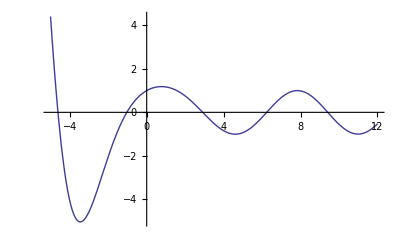

```mathematica
Plot[ⅇ^(-x/2)cos(x)+sin(x),{x,-5,12}]
```

Using starting guesses read off this plot, say {-5,-2,2,6,9}, use Newton's method (FindRoot) to produce a Table of accurate roots.

```mathematica
Table[FindRoot[ⅇ^(-x/2) cos(x)+sin(x),{x,n},WorkingPrecision->20],{n,{-5,-2,2,6,9}}]
```

{{x→-4.6131127603053817982},{x→-1.0328421509347170102},{x→2.9125828315219972204},{x→6.2390355478589685471},{x→9.4157542919845375202}}

Alternatively,

```mathematica
FindRoot[ⅇ^(-x/2) cos(x)+sin(x),{x,{-5,-2,2,6,9}},WorkingPrecision->20]
```

{x→{-4.613112760305381798,-1.0328421509347170102,2.91258283152199722,6.239035547858968547,9.4157542919845375202}}

For x≫1 ⅇ^(-x/2)cos(x)+sin(x)→sin(x) so the roots will be near n π with n∈ℤ,

```mathematica
Reduce[sin(x)==0,x]
```

c_1∈ℤ∧(x==2 π c_1∨x==2 π c_1+π)

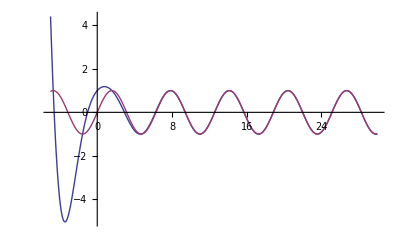

```mathematica
Plot[{ⅇ^(-x/2)cos(x)+sin(x),sin(x)},{x,-5,30}]
```

(LetteredPart) Compute the series expansions of

𝒮=(1+∑_(i=1)^4 a_i x^i)^n

and

ℰ=exp(n∑_(i=1)^4 a_i x^i)

to 5^th order in x using Series. Show that replacing n^k→n!/(n-k)! in the series for ℰ yields the series of 𝒮. (⚠ You need to expand the series for ℰ before applying the replacement rule.) [4 marks]

Answer: Compute the series expansion of 𝒮.

```mathematica
𝓈=(1+∑_(i=1)^4 Subscript[a, i] x^i)^n+O[x]^5
```

1+n a_1 x+(1/2 (n-1) n a_1^2+n a_2) x^2+(1/6 (n-2) (n-1) n a_1^3+(n-1) n a_2 a_1+n a_3) x^3+(1/24 (n-3) (n-2) (n-1) n a_1^4+1/2 (n-2) (n-1) n a_2 a_1^2+1/2 (n-1) n (a_2^2+2 a_1 a_3)+n a_4) x^4+O(x^5)

One could use Series instead.

```mathematica
Series[(1+∑_(i=1)^4 Subscript[a, i] x^i)^n,{x,0,4}]
```

1+n a_1 x+(1/2 (n-1) n a_1^2+n a_2) x^2+(1/6 (n-2) (n-1) n a_1^3+(n-1) n a_2 a_1+n a_3) x^3+(1/24 (n-3) (n-2) (n-1) n a_1^4+1/2 (n-2) (n-1) n a_2 a_1^2+1/2 (n-1) n (a_2^2+2 a_1 a_3)+n a_4) x^4+O(x^5)

Compute and Expand the series expansion of ℰ.

```mathematica
ℯ=exp(n∑_(i=1)^4 Subscript[a, i] x^i)+O[x]^5//Expand
```

1+n a_1 x+1/2 (n^2 a_1^2+2 n a_2) x^2+1/6 (n^3 a_1^3+6 n^2 a_2 a_1+6 n a_3) x^3+1/24 (n^4 a_1^4+12 n^3 a_2 a_1^2+24 n^2 a_3 a_1+12 n^2 a_2^2+24 n a_4) x^4+O(x^5)

Substitute n^k→n!/(n-k)! (you could also do this using four separate replacement rules).

```mathematica
ℯ/.n^k_->(n!)/((n-k)!)
```

1+n a_1 x+1/2 ((n! a_1^2)/((n-2)!)+2 n a_2) x^2+1/6 ((n! a_1^3)/((n-3)!)+(6 n! a_2 a_1)/((n-2)!)+6 n a_3) x^3+1/24 ((n! a_1^4)/((n-4)!)+(12 n! a_2 a_1^2)/((n-3)!)+(24 n! a_3 a_1)/((n-2)!)+(12 n! a_2^2)/((n-2)!)+24 n a_4) x^4+O(x^5)

Check that the two series are identical up 5^th order.

```mathematica
%-𝓈
```

O(x^5)

(LetteredPart) The following expression gives the intensity of light transmitted through a film after multiple reflections at the surfaces of the film:

(∑_(n=0)^∞ r^n cos(n θ))^2+(∑_(n=0)^∞ r^n sin(n θ))^2==(|∑_(n=0)^∞ (r ⅇ^(ⅈ θ))^n|)^2,

where 0<r<1.

(RomanPart) Compute and fully simplify each sum on the left-hand side of equation (DisplayFormulaNumbered) separately and then square them, add them together, and simplify the result. [2 marks]

Answer: Compute and simplfy the first sum.

```mathematica
cs=∑_(n=0)^∞ r^n cos(n θ)//FullSimplify
```

(1-r cos(θ))/(r^2-2 cos(θ) r+1)

Compute and simplfy the second sum.

```mathematica
ss=∑_(n=0)^∞ r^n sin(n θ)//FullSimplify
```

(r sin(θ))/(r^2-2 cos(θ) r+1)

Square them and add them together.

```mathematica
cs^2+ss^2//FullSimplify
```

1/(r^2-2 cos(θ) r+1)

(RomanPart) Compute the (geometric) sum on the right-hand side of equation (DisplayFormulaNumbered) and verify that equation is satisfied. [2 marks]

Answer: Compute the (geometric) sum on the right-hand side of equation (DisplayFormulaNumbered).

```mathematica
es=∑_(n=0)^∞ (r ⅇ^(ⅈ θ))^n
```

1/(1-ⅇ^(ⅈ θ) r)

Verify that equation (DisplayFormulaNumbered) is satisfied.

```mathematica
(∑_(n=0)^∞ r^n ⅇ^(ⅈ n θ))(∑_(n=0)^∞ r^n ⅇ^(-ⅈ n θ))//FullSimplify
```

1/(r^2-2 cos(θ) r+1)

(LetteredPart) The (scaled) Maxwellian speed distribution function

n(v)=4/(√π)  v^2 ⅇ^(-v^2),

gives the fraction of particles with speed between v and v+ⅆv.

(RomanPart) Plot n(v) over 0≤v≤10. [1 mark]

Answer: Define the Maxwellian speed distribution function.

```mathematica
n(v_)=4/(√π)  v^2 ⅇ^(-v^2);
```

Plot n(v) over 0≤v≤10.

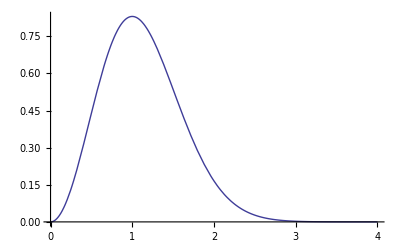

```mathematica
Plot[n(v),{v,0,4}]
```

(RomanPart) At what speed v is n(v) a maximum? [1 mark]

Answer: To determine the speed v for which n_v is a maximum, solve n'(v)==0.

```mathematica
D[n(v), v]//Simplify
```

-(8 ⅇ^(-v^2) v (v^2-1))/(√π)

```mathematica
Solve[%==0,v]
```

{{v→-1},{v→0},{v→1}}

Since v≥0, n_v is a maximum at v=1.

(RomanPart) Check that the distribution is correctly normalised, that is ∫_0^∞ n(v)ⅆv==1. [1 mark]

Answer: Computing

```mathematica
∫_0^∞ n(v)ⅆv==1
```

True

verifies that the distribution is correctly normalised.

(RomanPart) Define the expectation value ⟨v^α⟩==∫_0^∞ v^α n(v)ⅆv. Compute the average speed, ⟨v⟩, and the root mean square (rms) speed √⟨v^2⟩. Which is larger, ⟨v⟩ or √⟨v^2⟩? [2 marks]

Answer: Define the expectation value.

```mathematica
⟨v^(k_.)⟩:=∫_0^∞ v^k n(v)ⅆv
```

Note that this integral can be computed in closed form for k>-3.

```mathematica
Assuming[k>-3,∫_0^∞ v^k n(v)ⅆv]
```

(2 Γ((k+3)/2))/(√π)

Compute the average speed,

```mathematica
⟨v⟩
```

2/(√π)

and the root mean square (rms) speed,

```mathematica
√⟨v^2⟩
```

√(3/2)

Check that √⟨v^2⟩>⟨v⟩.

```mathematica
√⟨v^2⟩>⟨v⟩
```

True

Exercise. A question on determinants, eigenvalues, real-symmetric matrices. [12 marks]

Moments of inertia are used in various mechanics problems involving rotational motion. For example, one could consider the oscillations of a triangular plate as a rigid body pendulum with a fixed vertex.

```mathematica
Manipulate[Graphics[GeometricTransformation[{{Polygon[{{0,0},{1,0},{-0.1,2}}],Red,AbsolutePointSize[5],Point[{-0.1,2}]}},RotationTransform[θ,{-0.1,2}]], Frame->False,PlotRange->{{-2.2,2.4},{-0.5,2.1}}],{{θ,0},-π/2,π/3}]
```

In this problem, the applications are not important. You will merely be asked, in part (a), to find the second-moment matrix (closely related to the moment-of-inertia matrix) for a triangle. In part (b), you will be asked to determine the equation for a certain ellipse inscribed in a triangle. In part (c), you will be asked to discover some (geometric) properties of the eigenvectors of the second-moment matrix of part (a).

Consider a triangle with vertices at the origin, at {1,0}, and at {w_1,w_2}. Its vertices are thus at

```mathematica
origin={0,0};A={1,0};W={w1,w2};
```

The centroid of the triangle has coordinates the average of those of the vertices.

```mathematica
centroid=1/3 (origin+A+W)
```

{(w1+1)/3,w2/3}

The second-moment matrix for a solid triangle about the centroid is given by

```mathematica
momIarea[i_,j_,{w1_,w2_}]:=Module[
{x,centroid={1/3 (w1+1),w2/3}},
Factor[∫_0^w2 (∫_((x[2] w1)/w2)^(1-((1-w1) x[2])/w2) (x[i]-centroid⟦i⟧) (x[j]-centroid⟦j⟧)ⅆx[1])ⅆx[2]]
]
```

```mathematica
Iarea=Table[momIarea[i,j,W],{i,1,2},{j,1,2}]
```

(1/36 (w1^2-w1+1) w2 | 1/72 (2 w1-1) w2^2
1/72 (2 w1-1) w2^2 | w2^3/36)

2. A question on determinants, eigenvalues, real-symmetric matrices (continued).

(LetteredPart) Find the second moment matrix Iparea when the first two vertices are as above, i.e. the origin and {1,0}, and when the third vertex W={w_1,w_2} is changed  to W_p={1-w_1,w_2}, i.e. it is reflected in the line x=1/2. Show that matrices Iarea and Iparea are similar. Are the eigenvalues of Iarea and Iparea the same? Are the eigenvectors the same? [3 marks]

Answer: Compute the moment matrix:

```mathematica
Iparea = Table[momIarea[i, j,{1-w1,w2}], {i, 1, 2}, {j, 1, 2}]
```

(1/36 (w1^2-w1+1) w2 | -1/72 (2 w1-1) w2^2
-1/72 (2 w1-1) w2^2 | w2^3/36)

```mathematica
ℛ=ReflectionMatrix[{-1,0}]
```

(-1 | 0
0 | 1)

```mathematica
Iparea==ℛ.Iarea.ℛ
```

True

Since the matrices are similar, they have the same eigenvalues. Usually the eigenvectors will be different.

It is possible that the students could show directly that the eigenvalues are the same.

```mathematica
Eigenvalues[Iarea]==Eigenvalues[Iparea]
```

True

(LetteredPart) Consider ellipses inscribed in a triangle. Steiner discovered that the one with maximum area is tangent to the sides of the triangle at the midpoints of its sides and the centre of the ellipse is at the centroid of the triangle. With the triangle with sides origin, A, W, as above, find the Cartesian equation of the ellipse f(x,y)==0 and write it in the (quadratic) form (x-c).H.(x-c)==constant where x={x,y} and c is the centroid of the triangle. Hint: The equation f(x,y)==0 can be found by evaluating a certain 4×4 determinant whose rows can be constructed using makeRow:

```mathematica
makeRow[{x_,y_},{xc_,yc_}]:={(x-xc)^2,(x-xc) (y-yc),(y-yc)^2,1};
```

and requiring the value of the determinant to be zero. H is the Jacobian matrix (matrix of second derivatives) of f(x,y). [3 marks]

Answer: Construct the matrix.

```mathematica
Simplify[{makeRow[{x,y},centroid],makeRow[A/2,centroid],makeRow[(A+W)/2,centroid],makeRow[W/2,centroid]}]
```

(1/9 (w1-3 x+1)^2 | 1/9 (w1-3 x+1) (w2-3 y) | (y-w2/3)^2 | 1
1/36 (1-2 w1)^2 | 1/18 (2 w1-1) w2 | w2^2/9 | 1
1/36 (w1+1)^2 | 1/36 (w1+1) w2 | w2^2/36 | 1
1/36 (w1-2)^2 | 1/36 (w1-2) w2 | w2^2/36 | 1)

Determine the equation for the ellipse:

```mathematica
f[{w1_,w2_},{x_,y_}]=Collect[Det[%],{x,y},Factor]
```

-1/144 x^2 w2^3-w2^3/576-1/144 (w1-1) y w2^2-1/144 (w1^2-w1+1) y^2 w2+x (w2^3/144+1/144 (2 w1-1) y w2^2)

Compute the Jacobian matrix (matrix of second derivatives):

```mathematica
H=D[f[{w1,w2},{x,y}], {{x,y},2}]
```

(-w2^3/72 | 1/144 (2 w1-1) w2^2
1/144 (2 w1-1) w2^2 | -1/72 (w1^2-w1+1) w2)

Determine the constant in the (quadratic) form ({x,y}-centroid).H.({x,y}-centroid)==constant.

```mathematica
({x,y}-centroid).H.({x,y}-centroid)-2f[{w1,w2},{x,y}]//Simplify
```

-w2^3/864

(LetteredPart) Plot the vertices of the triangle, and the in-ellipse, so that the plots can be manipulated on changing w_1 and w_2. [3 marks]

Answer:

```mathematica
triangle[w1_,w2_]:=Graphics[{Opacity[0.5],Polygon[{{0,0},{1,0},{w1,w2}}]}];
```

```mathematica
ellipse[w1_,w2_]:=ContourPlot[f[{w1,w2},{x,y}]==0,{x,-1/2,3/2},{y,0,3/2},PlotPoints->30];
```

```mathematica
Manipulate[Show[{triangle[w1,w2],ellipse[w1,w2]},PlotRange->{{-1/2,3/2},{0,3/2}}],{w1,0,1},{w2,1/4,3/2},SaveDefinitions->True]
```

(LetteredPart) Show that the matrices Iarea and H have the same eigenvectors. Hint: If A and B are diagonalizable matrices which commute, i.e. A.B==B.A, then A and B have the same eigenvectors. Remark: This gives a geometric interpretation of the principal axes of inertia. The principal axes are defined as the eigenvectors of the second moment matrix. [3 marks]

Answer: Since H and Iarea commute,

```mathematica
H.Iarea - Iarea.H//Simplify
```

(0 | 0
0 | 0)

(and are diagonalizable) they share eigenvectors.

Exercise. Some applications to physical problems. [10 marks]

(LetteredPart) Consider the generating function

```mathematica
g[t_,r_]:=(1-t)^-3 exp((t r)/(t-1))
```

(RomanPart) Compute the series expansion of g(t,r)=∑_(n=0)^∞ p_n(r) t^n up to O(t^4) to obtain a set of polynomials, {p_n(r)}_(n=0,1,2,3) of degree n in r. [1 mark]

Answer: Compute the series expansion.

```mathematica
gs=g[t,r]+O[t]^4
```

1+(3-r) t+(r^2/2-4 r+6) t^2+(-r^3/6+(5 r^2)/2-10 r+10) t^3+O(t^4)

Here is a list of the polynomials.

```mathematica
polys[r_]=CoefficientList[%,t]
```

{1,3-r,r^2/2-4 r+6,-r^3/6+(5 r^2)/2-10 r+10}

Assign p_i(r) to be the (i+1)^th polynomial.

```mathematica
Table[Subscript[p, i](r_)=polys[r]⟦i+1⟧,{i,0,3}]
```

{1,3-r,r^2/2-4 r+6,-r^3/6+(5 r^2)/2-10 r+10}

It can be shown that p_n(r)==L_n^2(r) where L_n^2(r), computed via LaguerreL, is a generalized Laguerre polynomial.

```mathematica
Table[{n,Subscript[L, n]^2(r)},{n,0,3}]//Expand
```

(0 | 1
1 | 3-r
2 | r^2/2-4 r+6
3 | -r^3/6+(5 r^2)/2-10 r+10)

(RomanPart) Show that these polynomials are linearly independent by computing the (Wronskian) determinant

|p_0(r) | p_1(r) | p_2(r) | p_3(r)
p_0'(r) | p_1'(r) | p_2'(r) | p_3'(r)
p_0''(r) | p_1''(r) | p_2''(r) | p_3''(r)
p_0^(3)(r) | p_1^(3)(r) | p_2^(3)(r) | p_3^(3)(r)|≠0 [1 mark]

Answer: The determinant can be computed directly.

```mathematica
|{{Subscript[p, 0](r), Subscript[p, 1](r), Subscript[p, 2](r), Subscript[p, 3](r)}, {Subscript[p, 0]'(r), Subscript[p, 1]'(r), Subscript[p, 2]'(r), Subscript[p, 3]'(r)}, {Subscript[p, 0]''(r), Subscript[p, 1]''(r), Subscript[p, 2]''(r), Subscript[p, 3]''(r)}, {Derivative[3][Subscript[p, 0]](r), Derivative[3][Subscript[p, 1]](r), Derivative[3][Subscript[p, 2]](r), Derivative[3][Subscript[p, 3]](r)}}|
```

1

This shows the set of polynomials is linearly independent for all r. Alternatively, compute the matrix by nesting ∂_r  over the polynomials,

```mathematica
NestList[f↦D[f, r],polys[r],Length[polys[r]]-1]
```

(1 | 3-r | r^2/2-4 r+6 | -r^3/6+(5 r^2)/2-10 r+10
0 | -1 | r-4 | -r^2/2+5 r-10
0 | 0 | 1 | 5-r
0 | 0 | 0 | -1)

and then compute the determinant

```mathematica
Det[%]
```

1

(RomanPart) Show that they are orthogonal with respect to the inner product

⟨f,g⟩:=∫_0^∞ f g ⅇ^-r r^2 ⅆr  [1 mark]

Answer: For the inner product,

```mathematica
⟨f_,g_⟩:=∫_0^∞ f g ⅇ^-r r^2 ⅆr
```

these polynomials are orthogonal.

```mathematica
Table[⟨Subscript[p, i](r),Subscript[p, j](r)⟩,{i,0,3},{j,0,3}]
```

(2 | 0 | 0 | 0
0 | 6 | 0 | 0
0 | 0 | 12 | 0
0 | 0 | 0 | 20)

Alternatively,

```mathematica
Outer[AngleBracket,polys[r],polys[r]]
```

(2 | 0 | 0 | 0
0 | 6 | 0 | 0
0 | 0 | 12 | 0
0 | 0 | 0 | 20)

(RomanPart) Compute the determinant of the matrix

(p_0(r_0) | p_0(r_1) | p_0(r_2) | p_0(r_3)
p_1(r_0) | p_1(r_1) | p_1(r_2) | p_1(r_3)
p_2(r_0) | p_2(r_1) | p_2(r_2) | p_2(r_3)
p_3(r_0) | p_3(r_1) | p_3(r_2) | p_3(r_3))

and Factor the result to find a simple condition under which it vanishes. [2 marks]

Answer: Compute and factor the determinant.

```mathematica
Table[polys[x],{x,{Subscript[r, 0],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3]}}]//Transpose
```

(1 | 1 | 1 | 1
3-r_0 | 3-r_1 | 3-r_2 | 3-r_3
r_0^2/2-4 r_0+6 | r_1^2/2-4 r_1+6 | r_2^2/2-4 r_2+6 | r_3^2/2-4 r_3+6
-r_0^3/6+(5 r_0^2)/2-10 r_0+10 | -r_1^3/6+(5 r_1^2)/2-10 r_1+10 | -r_2^3/6+(5 r_2^2)/2-10 r_2+10 | -r_3^3/6+(5 r_3^2)/2-10 r_3+10)

```mathematica
%//Det//Factor
```

1/12 (r_0-r_1) (r_0-r_2) (r_1-r_2) (r_0-r_3) (r_1-r_3) (r_2-r_3)

```mathematica
({{Subscript[p, 0](Subscript[r, 0]), Subscript[p, 0](Subscript[r, 1]), Subscript[p, 0](Subscript[r, 2]), Subscript[p, 0](Subscript[r, 3])}, {Subscript[p, 1](Subscript[r, 0]), Subscript[p, 1](Subscript[r, 1]), Subscript[p, 1](Subscript[r, 2]), Subscript[p, 1](Subscript[r, 3])}, {Subscript[p, 2](Subscript[r, 0]), Subscript[p, 2](Subscript[r, 1]), Subscript[p, 2](Subscript[r, 2]), Subscript[p, 2](Subscript[r, 3])}, {Subscript[p, 3](Subscript[r, 0]), Subscript[p, 3](Subscript[r, 1]), Subscript[p, 3](Subscript[r, 2]), Subscript[p, 3](Subscript[r, 3])}})//Det//Factor
```

1/12 (r_0-r_1) (r_0-r_2) (r_1-r_2) (r_0-r_3) (r_1-r_3) (r_2-r_3)

Clearly the determinant vanishes if any r_i==r_j for 0≤i≠j≤3.

(LetteredPart) Consider the functional

```mathematica
ℱ[ψ[x_]]=1/2((ψ'(x))^2 +x^4 (ψ(x))^2-ℰ (ψ(x))^2);
```

(RomanPart) Use the Euler-Lagrange equation to find the differential equation related to this functional. [1 mark]

Answer: The Euler-Lagrange equation yields a second order differential equation,

```mathematica
EL=(∂ℱ[ψ[x]])/(∂ψ(x))-Subscript[ⅆ, x](∂ℱ[ψ[x]])/(∂ψ'(x))==0//Simplify
```

(x^4-ℰ) ψ(x)==ψ''(x)

(which is the Schrödinger equation for the quartic oscillator).

The Rayleigh-Ritz variational method applied to the differential equation in part (i) requires stationary values of the functional

```mathematica
ℰ[ϕ_]:=(∫_(-∞)^∞ (((∂ϕ)/(∂x))^2 +x^4 ϕ^2)ⅆx)/(∫_(-∞)^∞ ϕ^2 ⅆx)
```

where ϕ is an approximate solution leading to an upper bound for the (lowest) eigenvalue. The boundary condition is ψ(x)==0 as x→±∞.

(RomanPart) Explain why ϕ_β(x)=ⅇ^(- x^2)  (1+β x^2) is a suitable one-parameter trial function. [1 mark]

Answer: It satisfies the boundary condition, ψ(x)==0 as x→±∞, it is qualitatively of the expected form (it is symmetric in x), and it leads to integrals that can be computed exactly.

(RomanPart) Determine the optimal value for β, the corresponding eigenvalue ℰ, and plot ϕ_β(x). [3 marks]

Answer: For the one-parameter trial function,

```mathematica
Subscript[ϕ, β_](x_):=ⅇ^(- x^2)  (1+β x^2)
```

the eigenvalue is

```mathematica
λs=ℰ[Subscript[ϕ, β](x)]//Factor
```

(217 β^2-8 β+304)/(16 (3 β^2+8 β+16))

Stationary values of this functional,

```mathematica
Solve[D[λs, β]==0]
```

{{β→4/11 (-4-3 √3)},{β→4/11 (-4+3 √3)}}

with numerical values,

```mathematica
βs=N[%]
```

{{β→-3.34406},{β→0.434965}}

leads to the following eigenvalues.

```mathematica
λs/.βs
```

{7.5601,1.0649}

The smallest value is an upper-bound for the lowest eigenvalue (The exact value is ℰ_0=1.060362090… The second eigenvalue is an upper bound to the next-lowest eigenvalue for symmetric solutions, the ℰ_2=7.455697937…). Here is a plot of the two lowest (unnormalised) eigenfunctions.

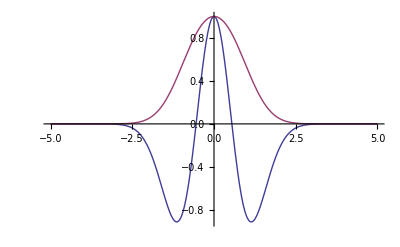

```mathematica
Plot[Evaluate[Tooltip/@(Subscript[ϕ, β](x)/.βs)],{x,-5,5}]
```

The ground state, corresponding to ℰ_0, has no nodes, and the first excited symmetric solution, corresponding to ℰ_2, has 2 nodes.

Exercise. A question on differential equations. [13 marks]

Consider the differential equation

a'==w,
w'==1/a^3-1.

(LetteredPart) Find the equilibrium solutions of equation (DisplayFormulaNumbered), and classify if they are unstable, neutrally stable, or something else. [3 marks]

Answer: From the first d.e., w=0 at any equilibrium. From the second d.e. a=1 and thus (a=1,w=0) is the only equilibrium. The Jacobian matrix is

```mathematica
J=D[{w,1/a^3-1}, {{a,w}}]
```

(0 | 1
-3/a^4 | 0)

```mathematica
JatEquilibrium=J/.{a->1}
```

(0 | 1
-3 | 0)

```mathematica
Eigenvalues[JatEquilibrium]
```

{ⅈ √3,-ⅈ √3}

Since the eigenvalues are pure imaginary, the equilibrium is neutrally stable.

(LetteredPart) Show that, for any solution of the system, the quantity

ℰ(a,w):=1/2 (w^2+1/a^2)+a

is constant along any trajectory. [3 marks]

Answer: From the first d.e., w=0 at any equilibrium. From the second d.e. a=1 and (a=1,w=0) is the only equilibrium. For

```mathematica
ℰ[a_,w_]:=1/2 (w^2+1/a^2)+a
```

the Jacobian matrix is

```mathematica
Factor[D[ℰ[a[t],D[a[t], t]], t]]
```

(a'(t) (a''(t) (a(t))^3+(a(t))^3-1))/(a(t))^3

Since this vanishes when the d.e. for a(t) is satisfied,

```mathematica
%/.a''(t)->1/(a(t))^3-1//Simplify
```

0

we have shown that ℰ is constant.

(LetteredPart) Show a ContourPlot of ℰ(a,w) over an appropriate region of the half-plane {(a,w)|a>0} showing several closed contours of ℰ. [3 marks]

Answer:

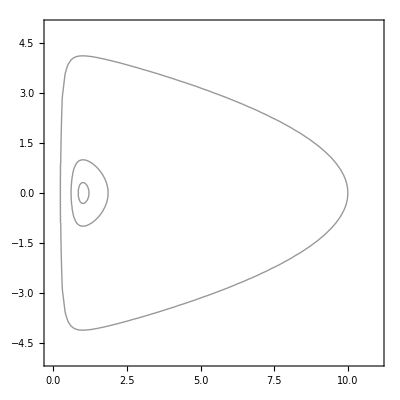

```mathematica
ContourPlot[ℰ[a,w],
{a,-0.1,11},{w,-5,5},Contours -> {1.55,2,10},ContourShading->False]
```

(LetteredPart) Denote the roots of the cubic for a given by ℰ(a,0) by -a_s, a_n and a_x. When there are 3 real roots, it can be shown (but you need not in this exam) that -1/2<-a_s<0<a_n<1<a_x. The period of the closed orbit for a_n<a_s<a_x is given by period[a_s] where

```mathematica
period[a_]:=-(2 (4 a^3 EllipticK[(2 √(1-8 a^3))/(4 a^3+√(1-8 a^3)+1)]-(4 a^3+√(1-8 a^3)+1) EllipticE[(2 √(1-8 a^3))/(4 a^3+√(1-8 a^3)+1)]))/(√2 a √(4 a^3+√(1-8 a^3)+1))
```

The parameter a_s has the physically relevant range 0<a_s<1/2. Furthermore, you are given a_s, a_x and a_n are related by

a_x==(1+√(1-8 a_s^3))/(4 a_s^2),
a_n==(1-√(1-8 a_s^3))/(4 a_s^2).

Find a_s in terms of a_x. Find the first two terms in a Series approximation to the period expanding about a_x==1. [4 marks]

Answer: Solve for a_s.

```mathematica
Solve[Subscript[a, x]==(1+√(1-8 Subscript[a, s]^3))/(4 Subscript[a, s]^2),Subscript[a, s]]
```

{{a_s→(-√(8 a_x^3+1)-1)/(4 a_x^2)},{a_s→(√(8 a_x^3+1)-1)/(4 a_x^2)}}

Only the positive root is relevant. Compute the series expansion of a_s about a_x==1 to sufficient order.

```mathematica
(Subscript[a, s]/.Last[%])+O[Subscript[a, x],1]^4
```

1/2-1/6 (a_x-1)^2+2/9 (a_x-1)^3+O((a_x-1)^4)

Compute the period.

```mathematica
period[%]
```

(2 π)/(√3)+(5 π (a_x-1)^2)/(6 √3)+O((a_x-1)^3)

END OF PAPER